## Initial Simulation

```mathematica
Sim[nParticles_,xParticles_,m_,length_]:={
Clear[xPos,trajData];

trajData={};
vTotalArray={};
F=0;
dpTotal=0;
nParticlesUsed=nParticles;
xParticlesUsed=xParticles[[1;;nParticlesUsed]];

For[i=1,i<=nSteps,i++,
v={vTherm,vTherm,vTherm};
vTotal=Sqrt[v[[1]]^2+v[[2]]^2+v[[3]]^2];
AppendTo[vTotalArray,vTotal];

For[n=1,n<=nParticlesUsed,n++,
xPos=xParticlesUsed[[n]][[i]];
xPos+=v dt;

If[xPos[[1]]<0,xPos[[1]]=-xPos[[1]];dp=Abs[2 m v[[1]]];dpTotal+=dp;v[[1]]=-v[[1]];];
If[xPos[[1]]>length,xPos[[1]]=2*length-xPos[[1]];dp=Abs[2 m v[[1]]];dpTotal+=dp;v[[1]]=-v[[1]];];
If[xPos[[2]]<0,xPos[[2]]=-xPos[[2]];dp=Abs[2 m v[[2]]];dpTotal+=dp;v[[2]]=-v[[2]];];
If[xPos[[2]]>length,xPos[[2]]=2*length-xPos[[2]];dp=Abs[2 m v[[2]]];dpTotal+=dp;v[[2]]=-v[[2]];];
If[xPos[[3]]<0,xPos[[3]]=-xPos[[3]];dp=Abs[2 m v[[3]]];dpTotal+=dp;v[[3]]=-v[[3]];];
If[xPos[[3]]>length,xPos[[3]]=2*length-xPos[[3]];dp=Abs[2 m v[[3]]];dpTotal+=dp;v[[3]]=-v[[3]];];

AppendTo[xParticlesUsed[[n]],xPos];
];

];

F+=dpTotal/time;
}
```

total force: 8.91881×10^-20 N

total pressure: 1.48647×10^-24 Pa

compressibility: 0.985643

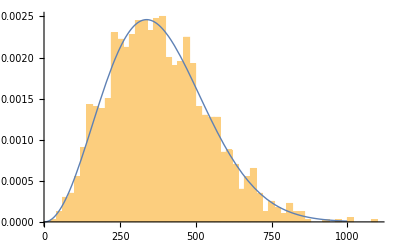

```mathematica
RT1=8.314*273; (*units J/mol = (kg m2/s2)/mol*)
M=39.9/1000; (*molar mass: units kg*)
vTherm:=Random[NormalDistribution[0,Sqrt[(RT1)/(M)]]] (*units m/s*)
m=6.6335209*(10^(-26)); (*atomic mass of Argon in kg*)

length=100;
nParticles=400;
time=100; (*units sec*)
dt=.05;
nSteps=Round[time/dt];

xParticles={};
For[i=1,i<=nParticles,i++,
AppendTo[xParticles,{{RandomReal[{0,length}],RandomReal[{0,length}],RandomReal[{0,length}]}}];
]

Sim[nParticles,xParticles,m,length];

area=6*(length^2);
V1=length^3;
P1=F/area;
n=nParticlesUsed/(6.02*(10^23));
Z=(P1 V1)/(n RT1);

Print["total force: ",F," N"]
Print["total pressure: ",P1," Pa"]
Print["compressibility: ", Z]

σ=((RT1)/M)^0.5;
MaxwellCurve=Plot[PDF[MaxwellDistribution[σ],x],{x,0,1000},PlotRange->{{0,1000},{0,.0035}},PlotStyle->Thick];
vTotalDist=Histogram[vTotalArray,bins=50,"PDF"];
Show[vTotalDist,MaxwellCurve]
```

```mathematica
RT1=8.314*273; (*units J/mol = (kg m2/s2)/mol*)
M=39.9/1000; (*molar mass: units kg*)
vTherm:=Random[NormalDistribution[0,Sqrt[(RT1)/(M)]]] (*units m/s*)
m=6.6335209*(10^(-26)); (*atomic mass of Argon in kg*)

nParticles=400;
length=1000;
time=100; (*units sec*)
dt=.15;
nSteps=Round[time/dt];

Sim[nParticles,xParticles,m,length];

animationArray={};
For[i=1,i<=nSteps+1,i++,
positionAllParticles={};
For[n=1,n<=nParticlesUsed,n++,
position=xParticlesUsed[[n]][[i]];
AppendTo[positionAllParticles,position];
];
AppendTo[animationArray,positionAllParticles]
]
```

```mathematica
v=Map[Point,animationArray];
animation=Animate[Graphics3D[{White,v[[i]]},PlotRange->{{0,length},{0,length},{0,length}}],{i,1,Length[v],1},AnimationRate->100,RefreshRate->100,DisplayAllSteps->True];
```

```mathematica
Export["C:\\Users\\prana\\OneDrive - The University of Texas at Austin\\Desktop\\Spring 2022\\comp chem\\gasanimation.avi",animation]
```

C:\Users\prana\OneDrive - The University of Texas at Austin\Desktop\Spring 2022\comp chem\gasanimation.avi

## Average Z Factor

```mathematica
ZSim[N1_,N2_,Nstep_,xParticles_,m_,length_,nRuns_]:={
ZarrayDiffNs={};
For[o=N1,o<=N2,o+=Nstep,
Zarray={};
For[k=1,k<=nRuns,k++,
Clear[xPos,trajData];

trajData={};
vTotalArray={};
F=0;
dpTotal=0;
nParticlesUsed=o;
xParticlesUsed=xParticles[[1;;nParticlesUsed]];

For[i=1,i<=nSteps,i++,
v={vTherm,vTherm,vTherm};
vTotal=Sqrt[v[[1]]^2+v[[2]]^2+v[[3]]^2];
AppendTo[vTotalArray,vTotal];

For[n=1,n<=nParticlesUsed,n++,
xPos=xParticlesUsed[[n]][[i]];
xPos+=v dt;

If[xPos[[1]]<0,xPos[[1]]=-xPos[[1]];dp=Abs[2 m v[[1]]];dpTotal+=dp;v[[1]]=-v[[1]];];
If[xPos[[1]]>length,xPos[[1]]=2*length-xPos[[1]];dp=Abs[2 m v[[1]]];dpTotal+=dp;v[[1]]=-v[[1]];];
If[xPos[[2]]<0,xPos[[2]]=-xPos[[2]];dp=Abs[2 m v[[2]]];dpTotal+=dp;v[[2]]=-v[[2]];];
If[xPos[[2]]>length,xPos[[2]]=2*length-xPos[[2]];dp=Abs[2 m v[[2]]];dpTotal+=dp;v[[2]]=-v[[2]];];
If[xPos[[3]]<0,xPos[[3]]=-xPos[[3]];dp=Abs[2 m v[[3]]];dpTotal+=dp;v[[3]]=-v[[3]];];
If[xPos[[3]]>length,xPos[[3]]=2*length-xPos[[3]];dp=Abs[2 m v[[3]]];dpTotal+=dp;v[[3]]=-v[[3]];];

AppendTo[xParticlesUsed[[n]],xPos];
];

];

F+=dpTotal/time;

area=6*(length^2);
V1=length^3;
P1=F/area;
n=nParticlesUsed/(6.02*(10^23));
Z=(P1 V1)/(n RT1);

AppendTo[Zarray,Z];
];
AppendTo[ZarrayDiffNs,{o,Zarray}]
];
ZmeanArrayDiffNs={};
For[l=1,l<=Length[ZarrayDiffNs],l++,
AppendTo[ZmeanArrayDiffNs,{ZarrayDiffNs[[l]][[1]],Mean[ZarrayDiffNs[[l]][[2]]]}]
]
}
```

```mathematica
RT1=8.314*273; (*units J/mol = (kg m2/s2)/mol*)
M=39.9/1000; (*molar mass: units kg*)
vTherm:=Random[NormalDistribution[0,Sqrt[(RT1)/(M)]]]; (*units m/s*)
m=6.6335209*(10^(-26)); (*atomic mass of Argon in kg*)

length=1000;
time=100; (*units sec*)
dt=.05;
nSteps=Round[time/dt];

xParticles={};
For[i=1,i<=nParticles,i++,
AppendTo[xParticles,{{RandomReal[{0,length}],RandomReal[{0,length}],RandomReal[{0,length}]}}];
];

N1=10;
N2=400;
Nstep=50;
nRuns=10;
ZSim[N1,N2,Nstep,xParticles,m,length,nRuns];
```

{{10,{0.725091,0.873854,0.59485,0.544474,0.556456,0.38008,0.539651,0.545317,0.525037,0.582723}},{60,{0.625777,1.01547,1.10147,0.980162,0.922318,1.19032,0.928935,0.965126,0.938165,0.760055}},{110,{0.874659,0.920349,0.936718,0.927582,1.10377,0.88241,0.976204,0.88866,0.921253,0.982461}},{160,{1.03677,0.937437,1.11874,0.914601,1.02169,0.9494,1.0262,0.981621,0.984859,0.955769}},{210,{1.00613,1.09039,1.00028,1.09616,0.991698,0.999206,1.05166,1.07421,0.948894,1.05822}},{260,{0.908719,1.01414,0.942677,0.904049,0.840882,0.982164,1.04421,0.967903,1.01745,0.917996}},{310,{1.00132,0.927494,1.07414,1.0515,1.10162,0.791974,0.967877,0.973124,0.993787,1.07805}},{360,{1.10046,1.1258,0.922234,1.15784,0.993503,1.04094,1.04768,1.10661,1.0236,1.08445}}}

{{10,0.586753},{60,0.942779},{110,0.941406},{160,0.99271},{210,1.03169},{260,0.954019},{310,0.996089},{360,1.06031}}

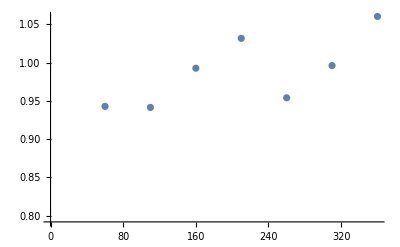

```mathematica
ZarrayDiffNs
ZmeanArrayDiffNs
ListPlot[ZmeanArrayDiffNs]
```

## Simulation with Different Volume

```mathematica
DiffVolume[originalLength_,multiplier_,nRuns_]:={
pressuresRatioVolume={};
lengthMultiplier=multiplier^(1/3);
length=lengthMultiplier*originalLength;

For[k=1,k<=nRuns,k++,
RT1=8.314*273; (*units J/mol = (kg m2/s2)/mol*)
M=39.9/1000; (*molar mass: units kg*)
vTherm:=Random[NormalDistribution[0,Sqrt[(RT1)/(M)]]];(*units m/s*)
m=6.6335209*(10^(-26)); (*atomic mass of Argon in kg*)

nParticles=400;
time=100; (*units sec*)
dt=.05;
nSteps=Round[time/dt];

xParticles={};
For[i=1,i<=nParticles,i++,
AppendTo[xParticles,{{RandomReal[{0,length}],RandomReal[{0,length}],RandomReal[{0,length}]}}];
];

Sim[nParticles,xParticles,m,length];

area=6*(length^2);
V2=length^3;
P2=F/area;
n=nParticlesUsed/(6.02*(10^23));
Z=(P2 V2)/(n RT1);

pressuresRatioVolume=AppendTo[pressuresRatioVolume, P1/P2];

σ=((RT1)/M)^0.5;
MaxwellCurve=Plot[PDF[MaxwellDistribution[σ],x],{x,0,1000},PlotRange->{{0,1000},{0,.0035}}];
vTotalDist=Histogram[vTotalArray,bins=50,"PDF"];
];

}
```

total force: 4.34085×10^-20

total pressure: 1.80869×10^-25

compressibility: 0.959438

P1/P2 = 8.28099

V2/V1 = 8

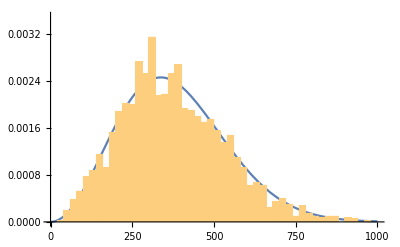

```mathematica
DiffVolume[100,8,1];

Print["total force: ",F]
Print["total pressure: ",P2]
Print["compressibility: ", Z]
Print["P1/P2 = ", P1/P2]
Print["V2/V1 = ", V2/V1]

Show[MaxwellCurve,vTotalDist]
```

Below is the result if the simulation is run 10 times and the average pressure ratio is taken.

```mathematica
multiplierVolume=8;
nRuns=10;
```

```mathematica
DiffVolume[100,multiplierVolume,nRuns];
```

```mathematica
Print[pressuresRatioVolume]
```

{7.89328,7.26403,9.67065,7.92187,7.69867,8.26179,7.91543,7.13317,8.76449,6.85595}

```mathematica
averagePressureRatioVolume=Mean[pressuresRatioVolume]
Print["variation from ideal: ",Abs[((averagePressureRatioVolume-multiplierVolume)/multiplierVolume )*100],"%"]
```

7.93793

variation from ideal: 0.77584%

## Simulation with Different Temperature

```mathematica
DiffTemp[originalTemp_,multiplier_,nRuns_]:={
pressuresRatioTemp={};
RT2=multiplier*8.314*originalTemp; (*units J/mol = (kg m2/s2)/mol*)

For[k=1,k<=nRuns,k++,
M=39.9/1000; (*molar mass: units kg*)
vTherm:=Random[NormalDistribution[0,Sqrt[(RT2)/(M)]]];(*units m/s*)
m=6.6335209*(10^(-26)); (*atomic mass of Argon in kg*)

length=100;
nParticles=400;
time=100; (*units sec*)
dt=.05;
nSteps=Round[time/dt];

xParticles={};
For[i=1,i<=nParticles,i++,
AppendTo[xParticles,{{RandomReal[{0,length}],RandomReal[{0,length}],RandomReal[{0,length}]}}];
];

Sim[nParticles,xParticles,m,length];

area=6*(length^2);
V1=length^3;
P2=F/area;
n=nParticlesUsed/(6.02*(10^23));
Z=(P2 V1)/(n RT2);

pressuresRatioTemp=AppendTo[pressuresRatioTemp, P1/P2];

σ=((RT2)/M)^0.5;
MaxwellCurve=Plot[PDF[MaxwellDistribution[σ],x],{x,0,1800},PlotRange->{{0,1800},{0,.0035}}];
vTotalDist=Histogram[vTotalArray,bins=30,"PDF"];
];
}
```

total force: 2.69011×10^-19

total pressure: 4.48351×10^-24

compressibility: 0.990971

P1/P2 = 0.331541

T1/T2 = 0.333333

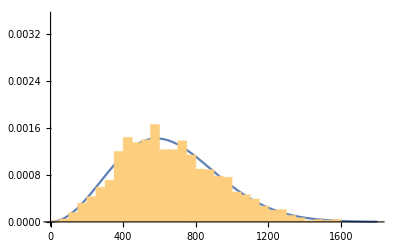

```mathematica
DiffTemp[273,3,1];

Print["total force: ",F]
Print["total pressure: ",P2]
Print["compressibility: ", Z]
Print["P1/P2 = ", P1/P2]
Print["T1/T2 = ", RT1/RT2]

Show[MaxwellCurve,vTotalDist]
```

Below is the result if the simulation is run 10 times and the average pressure ratio is taken.

```mathematica
multiplierTemp=3;
nRuns=10;
```

```mathematica
DiffTemp[273,multiplierTemp,nRuns];
```

```mathematica
Print[pressuresRatioTemp]
```

{0.357164,0.310868,0.317409,0.358936,0.298064,0.330713,0.343533,0.335827,0.303814,0.350567}

```mathematica
averagePressureRatioTemp=Mean[pressuresRatioTemp]
Print["variation from ideal: ",Abs[((averagePressureRatioTemp-(1/multiplierTemp))/(1/multiplierTemp) )*100],"%"]
```

0.33069

variation from ideal: 0.793144%

## Isothermal Compression

```mathematica
IsothermalCE[nParticles_,h1_,h2_,hstep_,m_,length_]:={
PVarray={};
Zarray={};

For[h=h1,h>=h2,h+=hstep,
Clear[xPos,trajData];
xParticles={};

trajData={};
vTotalArray={};
F=0;
dpTotal=0;

For[o=1,o<=nParticles,o++,
AppendTo[xParticles,{{RandomReal[{0,length}],RandomReal[{0,length}],RandomReal[{0,h}]}}];
];

For[i=1,i<=nSteps,i++,
v={vTherm,vTherm,vTherm};
vTotal=Sqrt[v[[1]]^2+v[[2]]^2+v[[3]]^2];
AppendTo[vTotalArray,vTotal];

For[n=1,n<=nParticles,n++,
xPos=xParticles[[n]][[i]];
xPos+=v dt;

If[xPos[[1]]<0,xPos[[1]]=-xPos[[1]];dp=Abs[2 m v[[1]]];dpTotal+=dp;v[[1]]=-v[[1]];];
If[xPos[[1]]>length,xPos[[1]]=2*length-xPos[[1]];dp=Abs[2 m v[[1]]];dpTotal+=dp;v[[1]]=-v[[1]];];
If[xPos[[2]]<0,xPos[[2]]=-xPos[[2]];dp=Abs[2 m v[[2]]];dpTotal+=dp;v[[2]]=-v[[2]];];
If[xPos[[2]]>length,xPos[[2]]=2*length-xPos[[2]];dp=Abs[2 m v[[2]]];dpTotal+=dp;v[[2]]=-v[[2]];];
If[xPos[[3]]<0,xPos[[3]]=-xPos[[3]];dp=Abs[2 m v[[3]]];dpTotal+=dp;v[[3]]=-v[[3]];];
If[xPos[[3]]>h,xPos[[3]]=2*h-xPos[[3]];dp=Abs[2 m v[[3]]];dpTotal+=dp;v[[3]]=-v[[3]];];

AppendTo[xParticles[[n]],xPos];
];

];

F+=dpTotal/time;

area=4*length*h+2*length^2;
V=h*length^2;
P=F/area;
n=nParticles/(6.02*(10^23));
Z=(P V)/(n RT);

AppendTo[PVarray,{V,P}];
AppendTo[Zarray,Z];
]
}
```

```mathematica
RT=8.314*273; (*units J/mol = (kg m2/s2)/mol*)
M=39.9/1000; (*molar mass: units kg*)
vTherm:=Random[NormalDistribution[0,Sqrt[(RT)/(M)]]]; (*units m/s*)
m=6.6335209*(10^(-26)); (*atomic mass of Argon in kg*)

nParticles=400;
time=100; (*units sec*)
dt=.05;
nSteps=Round[time/dt];

length=1000;
h1=1000;
h2=100;
hstep=-200;
nRuns=10;
IsothermalCE[nParticles,h1,h2,hstep,m,length];
```

```mathematica
Print[PVarray,Zarray]
```

{{1000000000,1.53888×10^-27},{800000000,1.84273×10^-27},{600000000,2.59661×10^-27},{400000000,4.08045×10^-27},{200000000,7.93431×10^-27}}{1.02039,0.977495,1.03305,1.08226,1.05221}

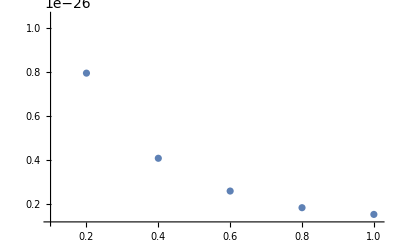

```mathematica
PVplot=ListPlot[PVarray,PlotRange->{{h2*length^2,1.01*h1*length^2},{1.2*^-27,1.05*^-26}}]
```

(1.50812×10^-18)/V

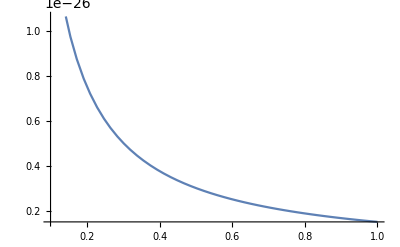

Theoretical work is 3.47258×10^-18 J.

```mathematica
Clear[V,W];
W[V_]=(n RT)/V
w=Integrate[W[V],{V,h2*length^2,h1*length^2}];
Plot[W[V],{V,h2*length^2,h1*length^2}]
Print["Theoretical work is ",w, " J."]
```

(1.58629×10^-18)/Vfit

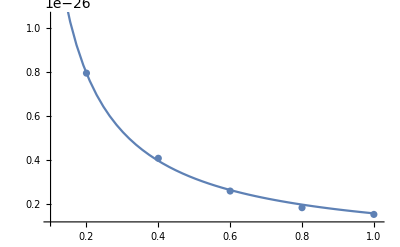

Estimated work calculated using the simulation is 3.65256×10^-18 J.

Percent error compared to the theoretical work is 5.18297%

```mathematica
regressionCoefficient=FindFit[PVarray,a/Vfit,a,Vfit];
Wfit[Vfit_]=a/Vfit/.{regressionCoefficient[[1]]}
wEstimate=Integrate[Wfit[x],{x,h2*length^2,h1*length^2}];
Show[PVplot,Plot[Wfit[Vfit],{Vfit,h2*length^2,h1*length^2}]]
Print["Estimated work calculated using the simulation is ",wEstimate, " J."]
Print["Percent error compared to the theoretical work is ",100*Abs[(wEstimate-w)/w],"%"]
```

## Collisions of Two Particles at a Time

```mathematica
Sim[nParticles_,m_,length_]:={
Clear[xPos,v,xParticles,vParticles];

F=0;
dpTotal=0;
collisiondata={};
isrunning={};

(*------------------------------------------------------------------------------------------------*)

xParticlesLoop={};
For[n=1,n<=nParticles,n++,
AppendTo[xParticlesLoop,{RandomReal[{0,length}],RandomReal[{0,length}],RandomReal[{0,length}]}];
];
xParticles={xParticlesLoop};

vTotalArray={};
vParticlesLoop={};
For[n=1,n<=nParticles,n++,
vTotal=Sqrt[vAdd[[1]]^2+vAdd[[2]]^2+vAdd[[3]]^2];
AppendTo[vParticlesLoop,{vTherm,vTherm,vTherm}];
AppendTo[vTotalArray,vTotal]
];
vParticles={vParticlesLoop};


(*------------------------------------------------------------------------------------------------*)


For[i=1,i<=nSteps,i++,
allParticlesAtOneTime={};
allVelocitiesAtOneTime={};


(*------------------------------------------------------------------------------------------------*)


positionsAtTime=xParticles[[i]];
distanceArray={};

For[k=1,k<=Length[positionsAtTime],k++,
firstParticlePos=positionsAtTime[[k]];
distanceWithEachParticle={};

For[l=1,l<=Length[positionsAtTime],l++,
If[l!=k,
secondParticlePos=positionsAtTime[[l]];
xdist=secondParticlePos[[1]]-firstParticlePos[[1]];
ydist=secondParticlePos[[2]]-firstParticlePos[[2]];
zdist=secondParticlePos[[3]]-firstParticlePos[[3]];
distance=Sqrt[xdist^2 + ydist^2 + zdist^2];
AppendTo[distanceWithEachParticle,{{k,l}, distance}];
];
];

AppendTo[distanceArray,distanceWithEachParticle];
];

collidingParticles={};
For[k=1,k<=Length[distanceArray],k++,
distancesWithParticleCenter=distanceArray[[k]];
For[l=1,l<=Length[distancesWithParticleCenter],l++,
If[distancesWithParticleCenter[[l]][[2]]<=2r,
AppendTo[collidingParticles,distancesWithParticleCenter[[l]][[1]]];
];
];
];

collidingParticles1Darray={};
For[k=1,k<=Length[collidingParticles],k++,
For[l=1,l<=Length[collidingParticles[[k]]],l++,
AppendTo[collidingParticles1Darray,collidingParticles[[k]][[l]]];
AppendTo[collidingParticles1Darray,collidingParticles[[k]][[l]]];
];
];
collidingParticles=DeleteDuplicates[collidingParticles1Darray];

AppendTo[collisiondata,collidingParticles];

If[Length[collidingParticles]==2,
AppendTo[isrunning,1];
particle1=collidingParticles[[1]];
particle2=collidingParticles[[2]];
v1=vParticles[[i]][[particle1]];
v2=vParticles[[i]][[particle2]];

vParticles[[i]][[particle1]]=v2;
vParticles[[i]][[particle2]]=v1;
];


(*------------------------------------------------------------------------------------------------*)


For[n=1,n<=nParticles,n++,
xPos=xParticles[[i]][[n]];
v=vParticles[[i]][[n]];
xPos+=v dt;

If[xPos[[1]]<0,xPos[[1]]=-xPos[[1]];dp=Abs[2 m v[[1]]];dpTotal+=dp;v[[1]]=-v[[1]];];
If[xPos[[1]]>length,xPos[[1]]=2*length-xPos[[1]];dp=Abs[2 m v[[1]]];dpTotal+=dp;v[[1]]=-v[[1]];];
If[xPos[[2]]<0,xPos[[2]]=-xPos[[2]];dp=Abs[2 m v[[2]]];dpTotal+=dp;v[[2]]=-v[[2]];];
If[xPos[[2]]>length,xPos[[2]]=2*length-xPos[[2]];dp=Abs[2 m v[[2]]];dpTotal+=dp;v[[2]]=-v[[2]];];
If[xPos[[3]]<0,xPos[[3]]=-xPos[[3]];dp=Abs[2 m v[[3]]];dpTotal+=dp;v[[3]]=-v[[3]];];
If[xPos[[3]]>length,xPos[[3]]=2*length-xPos[[3]];dp=Abs[2 m v[[3]]];dpTotal+=dp;v[[3]]=-v[[3]];];

AppendTo[allParticlesAtOneTime,xPos];
AppendTo[allVelocitiesAtOneTime,v];
vTotal=Sqrt[v[[1]]^2+v[[2]]^2+v[[3]]^2];
AppendTo[vTotalArray,vTotal];

];


(*------------------------------------------------------------------------------------------------*)


AppendTo[xParticles,allParticlesAtOneTime];
AppendTo[vParticles,allVelocitiesAtOneTime];

];

F+=dpTotal/time;

}
```

```mathematica
RT1=8.314*273; (*units J/mol = (kg m2/s2)/mol*)
M=39.9/1000; (*molar mass: units kg*)
vTherm:=Random[NormalDistribution[0,Sqrt[(RT1)/(M)]]] (*units m/s*)
m=6.6335209*(10^(-26)); (*atomic mass of Argon in kg*)
r=9.8*^-11; (*atomic radius of Argon in m*)

length=1*^-8;
nParticles=100;
time=2*^-11; (*units sec*)
dt=2*^-13;
nSteps=Round[time/dt];

Sim[nParticles,m,length];

area=6*(length^2);
V1=length^3;
P1=F/area;
n=nParticles/(6.02*(10^23));
Z=(P1 V1)/(n RT1);

Print["total force: ",F," N"]
Print["total pressure: ",P1," Pa"]
Print["compressibility: ", Z]

σ=((RT1)/M)^0.5;
MaxwellCurve=Plot[PDF[MaxwellDistribution[σ],x],{x,0,1000},PlotRange->{{0,1000},{0,.0035}},PlotStyle->Thick];
vTotalDist=Histogram[vTotalArray,bins=50,"PDF"];
Show[vTotalDist,MaxwellCurve];
```

Part::partd: Part specification vAdd⟦1⟧ is longer than depth of object.

Part::partd: Part specification vAdd⟦2⟧ is longer than depth of object.

Part::partd: Part specification vAdd⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

total force: 2.33015×10^-10 N

total pressure: 388358. Pa

compressibility: 1.03005

```mathematica
pointsize=2r/length
V1
VolParticles=nParticles(4/3)(Pi)(r)^3
availableV=V1-VolParticles
volumeRatio=availableV/V1
(P1 availableV) / (n RT1)
collisiondata
isrunning
```

0.0196

1/1000000000000000000000000

3.94246×10^-28

9.99606×10^-25

0.999606

1.02964

{{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{67,100},{},{},{52,95},{},{},{},{},{},{},{},{},{},{},{},{},{53,56},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{23,95},{},{},{},{},{},{},{49,84},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}}

{1,1,1,1,1}

```mathematica
v1
```

{-212.294,-101.2,370.235}

```mathematica
v2
```

{-76.1294,-54.3342,-341.931}

```mathematica
vParticles[[17]][[9]]
vParticles[[18]][[66]]
```

{-57.6035,-116.103,-186.36}

{-54.5129,-143.912,422.012}

```mathematica
v=Map[Point,xParticles];
animation=Animate[Graphics3D[{White,PointSize[pointsize],v[[i]]},PlotRange->{{0,length},{0,length},{0,length}}],{i,1,Length[v],1},AnimationRate->10,RefreshRate->100,DisplayAllSteps->True]
```

## Proving that Velocities Switch as Assumed for the Collisions Simulation

```mathematica
Clear[v1x,v2x,v1y,v2y,v1z,v2z];
sol=Solve[m v1[[1]]+m v2[[1]]==m v1x + m v2x&&0.5 m v1[[1]]^2+0.5 m v2[[1]]^2==0.5m v1x^2 + 0.5m v2x^2&& m v1[[2]]+m v2[[2]]==m v1y + m v2y&&0.5 m v1[[2]]^2+0.5 m v2[[2]]^2==0.5m v1y^2 + 0.5m v2y^2&&m v1[[3]]+m v2[[3]]==m v1z + m v2z&&0.5 m v1[[3]]^2+0.5 m v2[[3]]^2==0.5m v1z^2 + 0.5m v2z^2&&v1x!=v1[[1]], {v1x,v2x,v1y,v2y,v1z,v2z}]

finalSol={1,1,1,1,1,1};
For[i=1,i<=Length[sol],i++,
If[sol[[i]][[1]][[2]]!=v1[[1]],finalSol[[1]]=sol[[i]][[1]];];
If[sol[[i]][[2]][[2]]!=v2[[1]],finalSol[[2]]=sol[[i]][[2]];];
If[sol[[i]][[3]][[2]]!=v1[[2]],finalSol[[3]]=sol[[i]][[3]];];
If[sol[[i]][[4]][[2]]!=v2[[2]],finalSol[[4]]=sol[[i]][[4]];];
If[sol[[i]][[5]][[2]]!=v1[[3]],finalSol[[5]]=sol[[i]][[5]];];
If[sol[[i]][[6]][[2]]!=v2[[3]],finalSol[[6]]=sol[[i]][[6]];];
]
finalSolArray=finalSol/.Rule->List
v1x=finalSolArray[[1]][[2]]
v2x=finalSolArray[[2]][[2]]
v1y=finalSolArray[[3]][[2]]
v2y=finalSolArray[[4]][[2]]
v1z=finalSolArray[[5]][[2]]
v2z=finalSolArray[[6]][[2]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{{v1x→-204.708,v2x→-31.2912,v1y→8.18265,v2y→206.899,v1z→-235.141,v2z→148.155},{v1x→-204.708,v2x→-31.2912,v1y→206.899,v2y→8.18265,v1z→-235.141,v2z→148.155},{v1x→-204.708,v2x→-31.2912,v1y→8.18265,v2y→206.899,v1z→148.155,v2z→-235.141},{v1x→-204.708,v2x→-31.2912,v1y→206.899,v2y→8.18265,v1z→148.155,v2z→-235.141},{v1x→-31.2912,v2x→-204.708,v1y→8.18265,v2y→206.899,v1z→-235.141,v2z→148.155},{v1x→-31.2912,v2x→-204.708,v1y→206.899,v2y→8.18265,v1z→-235.141,v2z→148.155},{v1x→-31.2912,v2x→-204.708,v1y→8.18265,v2y→206.899,v1z→148.155,v2z→-235.141},{v1x→-31.2912,v2x→-204.708,v1y→206.899,v2y→8.18265,v1z→148.155,v2z→-235.141}}

{{v1x,-31.2912},{v2x,-204.708},{v1y,206.899},{v2y,8.18265},{v1z,-235.141},{v2z,148.155}}

-31.2912

-204.708

206.899

8.18265

-235.141

148.155

```mathematica
v1[[1]]
v2[[1]]
v1[[2]]
v2[[2]]
v1[[3]]
v2[[3]]
```

-204.708

-31.2912

8.18265

206.899

148.155

-235.141